```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis\\mNStar"]];
Print["(DescDir) Rawdata Directory: ",descDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\Prajwal\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\system"];
];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,"\\","desc.dat"],{Word,Word,Word,Number,Number,Number,Number,Word}];
runst=16;
runend=39;
Print["Runs in the list: ",runNum=descdat[[runst;;runend,4]]];(*11159,11369*)
Print["Size: ",runn=Dimensions[runNum][[1]]];
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis\mNStar

(DescDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\Prajwal\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\Prajwal\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\Prajwal\Dropbox\nEDM\system

Runs in the list: {13099,13101,13102,13103,13104,13105,13106,13107,13108,13109,13110,13111,13112,13132,13133,13134,13135,13136,13137,13138,13139,13140,13141,13142}

Size: 24

```mathematica
superdat={};
AccountingForm[TableForm[SetPrecision[superdat,10]]]
Print["Runs in the list: ",runNum2=descdat[[runst;;runend,4]]];
Print["Storage time in the list: ",ts2=descdat[[runst;;runend,7]]];
Print["Size: ",runn2=Dimensions[runNum2][[1]]];
For[runi=1,runi≤runn2,runi++,
metadatascr=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum2[[runi]],10,6],"\\",IntegerString[runNum2[[runi]],10,6],"_Meta5-2.dat"],metaStructure2];
superdat=AppendTo[superdat,{ts2[[runi]],Mean[Table[(PlusMinus[(metadatascr[[k]][[27]]+metadatascr[[k]][[28]]),Sqrt[(metadatascr[[k]][[27]]+metadatascr[[k]][[28]])]])/PlusMinus[(metadatascr[[k]][[30]]),Sqrt[(metadatascr[[k]][[30]])]],{k,3,Dimensions[metadatascr][[1]]}]]}];
];
superdat=Sort[superdat,#1[[1]]<#2[[1]]&];
expsuperdat=AccountingForm[TableForm[SetPrecision[superdat,10]]]
```

{}

Runs in the list: {13099,13101,13102,13103,13104,13105,13106,13107,13108,13109,13110,13111,13112,13132,13133,13134,13135,13136,13137,13138,13139,13140,13141,13142}

Storage time in the list: {380,365,350,335,320,305,290,275,260,245,230,215,200,170,155,140,125,110,95,80,65,50,35,180}

Size: 24

35.00000000 | 0.07740000000±0.00007700000000
50.00000000 | 0.06916900000±0.00007700000000
65.00000000 | 0.06022500000±0.00006500000000
80.00000000 | 0.05393200000±0.00006400000000
95.00000000 | 0.04886100000±0.00006000000000
110.0000000 | 0.04467900000±0.00005800000000
125.0000000 | 0.04059200000±0.00005400000000
140.0000000 | 0.03691600000±0.00005600000000
155.0000000 | 0.03418000000±0.00004900000000
170.0000000 | 0.03043800000±0.00005600000000
180.0000000 | 0.03049400000±0.00001600000000
200.0000000 | 0.02696400000±0.00004600000000
215.0000000 | 0.02498000000±0.0001200000000
230.0000000 | 0.02334600000±0.00004600000000
245.0000000 | 0.02193200000±0.00004800000000
260.0000000 | 0.02028100000±0.00004000000000
275.0000000 | 0.01857800000±0.00003900000000
290.0000000 | 0.01768400000±0.00003700000000
305.0000000 | 0.01640200000±0.00004200000000
320.0000000 | 0.01558200000±0.00003400000000
335.0000000 | 0.01492000000±0.00003700000000
350.0000000 | 0.01351400000±0.00003200000000
365.0000000 | 0.01358500000±0.00004400000000
380.0000000 | 0.01191460000±0.000003800000000

```mathematica
superdat2={};
gaps=Table[1,{k,1,runn2}];
Total[gaps]==Dimensions[superdat][[1]]
For[j=1,j≤Dimensions[gaps][[1]],j++,
superdat2=AppendTo[superdat2,Mean[Table[superdat[[j2]],{j2,Total[gaps[[1;;j]]]+1-gaps[[j]],Total[gaps[[1;;j]]]}]]];
];
expsuperdat2=AccountingForm[TableForm[SetPrecision[superdat2,10]]];
superdat3=superdat2+Table[{22.6,PlusMinus[0,.00004]},{k,1,Dimensions[superdat2][[1]]}];
expsuperdat3=AccountingForm[TableForm[SetPrecision[superdat3,10]]]
Export["expsuperdat2-Cu.dat",superdat3]
```

True

57.60000000 | 0.07740000000±0.00008700000000
72.60000000 | 0.06916900000±0.00008700000000
87.60000000 | 0.06022500000±0.00007600000000
102.6000000 | 0.05393200000±0.00007500000000
117.6000000 | 0.04886100000±0.00007200000000
132.6000000 | 0.04467900000±0.00007000000000
147.6000000 | 0.04059200000±0.00006700000000
162.6000000 | 0.03691600000±0.00006900000000
177.6000000 | 0.03418000000±0.00006300000000
192.6000000 | 0.03043800000±0.00006900000000
202.6000000 | 0.03049400000±0.00004300000000
222.6000000 | 0.02696400000±0.00006100000000
237.6000000 | 0.02498000000±0.0001300000000
252.6000000 | 0.02334600000±0.00006100000000
267.6000000 | 0.02193200000±0.00006200000000
282.6000000 | 0.02028100000±0.00005700000000
297.6000000 | 0.01857800000±0.00005600000000
312.6000000 | 0.01768400000±0.00005400000000
327.6000000 | 0.01640200000±0.00005800000000
342.6000000 | 0.01558200000±0.00005200000000
357.6000000 | 0.01492000000±0.00005400000000
372.6000000 | 0.01351400000±0.00005100000000
387.6000000 | 0.01358500000±0.00005900000000
402.6000000 | 0.01191500000±0.00004000000000

expsuperdat2-Cu.dat

FittedModel[0.074401 ⅇ^(-0.016828 t)+0.0625305 ⅇ^(-0.00409206 t)]

InterpolatingFunction[…]

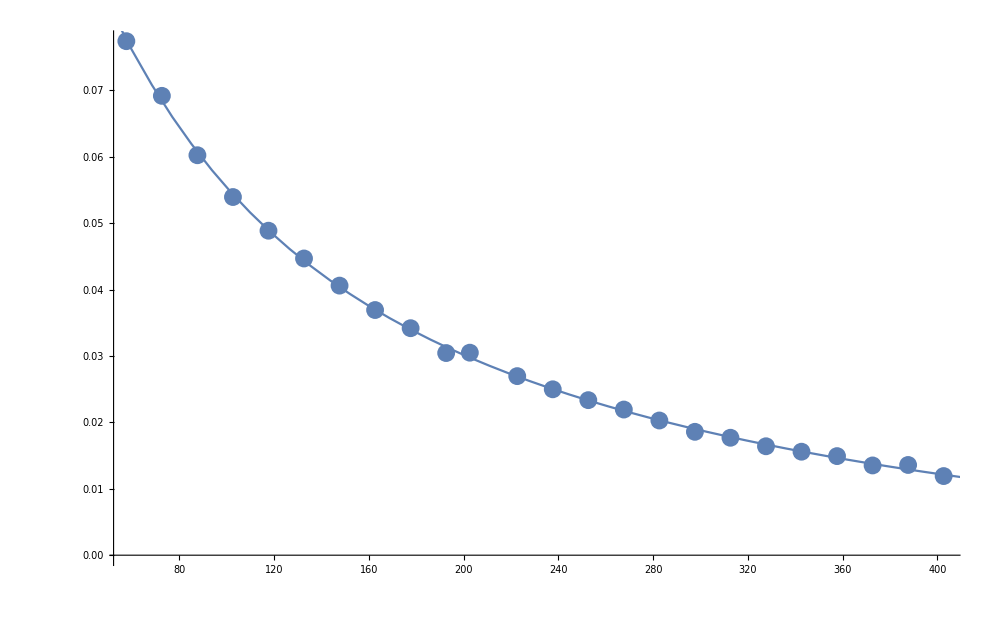

```mathematica
Clear[bb];
ptsuperdat3=Table[{superdat3[[k]][[1]],{superdat3[[k]][[2]][[1]],superdat3[[k]][[2]][[2]]}},{k,1,Dimensions[superdat3][[1]]}];
ftsuperdat3=Table[{superdat3[[k]][[1]],superdat3[[k]][[2]][[1]]},{k,1,Dimensions[superdat3][[1]]}];
Print[nlm0=NonlinearModelFit[ftsuperdat3,(bb Exp[t cc]+dd Exp[t ee]),{{bb,.1},{cc,-.1},{dd,.1},{ee,-.1}},t]]
nlm00=Interpolation[ftsuperdat3[[1;;runn2]],InterpolationOrder->1]
rat[x_]:=nlm0[x]/nlm01[x];
rat2[x_]:=nlm00[x]/nlm001[x];
rat3[x_]:=nlm0[x]/ftsuperdat3[[7;;15,2]];
Show[{
EDAListPlot[ptsuperdat3,ImageSize->1000,PlotRange->Full],
Plot[nlm0[xx],{xx,10,420}]
}]
```

```mathematica
ptseries1=Table[{superdat3[[k]][[1]],{superdat3[[k]][[2]][[1]],superdat3[[k]][[2]][[2]]}},{k,1,runn2}];
bdptseries=Part[ptseries1,{}];
ptseries2=DeleteCases[ptseries1,Alternatives@@bdptseries];
ftseries2=Transpose[{ptseries2[[;;,1]],ptseries2[[;;,2]][[;;,1]]}];
ptallseries=ptseries2;
ptallseries=Sort[ptallseries,#1[[1]]<#2[[1]]&]
ftallseries=ftseries2;
ftallseries=Sort[ftallseries,#1[[1]]<#2[[1]]&]
errallseries=Table[ptallseries[[k]][[2]][[2]],{k,1,Dimensions[ptallseries][[1]]}];
Print[nlm2=NonlinearModelFit[ftallseries,(bb Exp[t cc]+dd Exp[t ee]),{{bb,.1},{cc,-.1},{dd,.1},{ee,-.1}},t]];
AccountingForm[TableForm[SetPrecision[Table[{ptallseries[[k]][[1]],PlusMinus[ptallseries[[k]][[2]][[1]],ptallseries[[k]][[2]][[2]]]},{k,1,Dimensions[ptallseries][[1]]}],4]]];
Export["expsuperdat3-Cu.dat",Table[{ptallseries[[k]][[1]],PlusMinus[ptallseries[[k]][[2]][[1]],ptallseries[[k]][[2]][[2]]]},{k,1,Dimensions[ptallseries][[1]]}]];
nlm0["ParameterTable"]
Print["Sigmas: ",sigmas=(nlm2["FitResiduals"]/errallseries)]
Print["Chi^2/ndf: ",Total[((nlm2["FitResiduals"]/errallseries))^2]/(Dimensions[ftallseries][[1]]-2)]
nlm2["ANOVATable"]
nlm2["ParameterTable"]
Grid[Transpose[{#,nlm2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]
Show[{
EDAListPlot[ptallseries,PlotRange->Full,GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"t_Storage (s)","(N_↑+N_↓)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Red,Medium}],
Plot[{nlm2[xx],nlm2[xx]+nlm2["ParameterErrors"][[1]],nlm2[xx]-nlm2["ParameterErrors"][[1]]},{xx,10,420},Filling->{2->{3}},FillingStyle->{Opacity[.5],Blue},PlotStyle->{{Blue,Thickness[.005]},None,None}]
}]
```

{{57.6,{0.0774,0.000087}},{72.6,{0.069169,0.000087}},{87.6,{0.060225,0.000076}},{102.6,{0.053932,0.000075}},{117.6,{0.048861,0.000072}},{132.6,{0.044679,0.00007}},{147.6,{0.040592,0.000067}},{162.6,{0.036916,0.000069}},{177.6,{0.03418,0.000063}},{192.6,{0.030438,0.000069}},{202.6,{0.030494,0.000043}},{222.6,{0.026964,0.000061}},{237.6,{0.02498,0.00013}},{252.6,{0.023346,0.000061}},{267.6,{0.021932,0.000062}},{282.6,{0.020281,0.000057}},{297.6,{0.018578,0.000056}},{312.6,{0.017684,0.000054}},{327.6,{0.016402,0.000058}},{342.6,{0.015582,0.000052}},{357.6,{0.01492,0.000054}},{372.6,{0.013514,0.000051}},{387.6,{0.013585,0.000059}},{402.6,{0.011915,0.00004}}}

{{57.6,0.0774},{72.6,0.069169},{87.6,0.060225},{102.6,0.053932},{117.6,0.048861},{132.6,0.044679},{147.6,0.040592},{162.6,0.036916},{177.6,0.03418},{192.6,0.030438},{202.6,0.030494},{222.6,0.026964},{237.6,0.02498},{252.6,0.023346},{267.6,0.021932},{282.6,0.020281},{297.6,0.018578},{312.6,0.017684},{327.6,0.016402},{342.6,0.015582},{357.6,0.01492},{372.6,0.013514},{387.6,0.013585},{402.6,0.011915}}

FittedModel[0.074401 ⅇ^(-0.016828 t)+0.0625305 ⅇ^(-0.00409206 t)]

| Estimate | Standard Error | t-Statistic | P-Value
bb | 0.0625305 | 0.0048758 | 12.8247 | 4.16435×10^-11
cc | -0.00409206 | 0.000215743 | -18.9673 | 2.96403×10^-14
dd | 0.074401 | 0.00281088 | 26.469 | 4.84022×10^-17
ee | -0.016828 | 0.00166069 | -10.1332 | 2.53165×10^-9

Sigmas: {-2.57624,8.99062,-6.63398,-5.27292,-0.936566,4.93253,3.04882,-0.755583,3.19714,-13.1151,17.2524,0.97545,-0.27233,0.706968,3.06287,-0.56036,-7.51649,-1.89796,-4.52383,-0.791836,4.9091,-4.68228,11.4237,-5.23647}

Chi^2/ndf: 44.1175

| DF | SS | MS
Model | 4 | 0.0324159 | 0.00810396
Error | 20 | 3.57809×10^-6 | 1.78904×10^-7
Uncorrected Total | 24 | 0.0324194 | 
Corrected Total | 23 | 0.00793493 |

| Estimate | Standard Error | t-Statistic | P-Value
bb | 0.0625305 | 0.0048758 | 12.8247 | 4.16435×10^-11
cc | -0.00409206 | 0.000215743 | -18.9673 | 2.96403×10^-14
dd | 0.074401 | 0.00281088 | 26.469 | 4.84022×10^-17
ee | -0.016828 | 0.00166069 | -10.1332 | 2.53165×10^-9

AdjustedRSquared | 0.999868
AIC | -298.765
BIC | -292.875
RSquared | 0.99989

-Graphics-

```mathematica
finpt2=finpt
```

{{57.6,{0.0774,0.000087}},{72.6,{0.067864,0.000087}},{87.6,{0.060225,0.000076}},{102.6,{0.053932,0.000075}},{117.6,{0.048861,0.000072}},{132.6,{0.044329,0.00007}},{147.6,{0.040257,0.000067}},{162.6,{0.036916,0.000069}},{177.6,{0.03418,0.000063}},{192.6,{0.0312315,0.000069}},{202.6,{0.029849,0.000043}},{222.6,{0.026964,0.000061}},{237.6,{0.02498,0.00013}},{252.6,{0.023346,0.000061}},{267.6,{0.021932,0.000062}},{282.6,{0.020281,0.000057}},{297.6,{0.019222,0.000056}},{312.6,{0.017684,0.000054}},{327.6,{0.016402,0.000058}},{342.6,{0.015582,0.000052}},{357.6,{0.01465,0.000054}},{372.6,{0.013514,0.000051}},{387.6,{0.0127,0.000059}},{402.6,{0.011915,0.00004}}}

## Playing

```mathematica
runn2
finpt=Table[{ftallseries[[k]][[1]],{If[k==11||k==23||k==2,ftallseries[[k]][[2]]-15ptallseries[[k]][[2]][[2]],If[k==6||k==7||k==21,ftallseries[[k]][[2]]-5ptallseries[[k]][[2]][[2]],If[k==17||k==10,ftallseries[[k]][[2]]+11.5ptallseries[[k]][[2]][[2]],ftallseries[[k]][[2]]]]],ptallseries[[k]][[2]][[2]]}},{k,1,runn2}];
(***)
tslong={430,480,580,630,680,730,780,830,880,930,980,1030,1080};
longst=ReadList[StringJoin[AscDir,"\\",IntegerString[13145,10,6],"\\",IntegerString[13145,10,6],"_Meta5.edm"],metaStructure2];
For[k=1,k≤Dimensions[tslong][[1]],k++,
finpt=AppendTo[finpt,{tslong[[k]]+22.6,{N[(longst[[k]][[27]]+longst[[k]][[28]])],N[Sqrt[(longst[[k]][[27]]+longst[[k]][[28]])]]}/longst[[k]][[30]]}];
];
errallseries=Table[finpt[[k]][[2]][[2]],{k,1,Dimensions[finpt][[1]]}];
finpt=Table[{finpt[[k]][[1]],{
If[k==26,finpt[[k]][[2]][[1]]+3finpt[[k]][[2]][[2]],
If[k==27||k==28||k==29||k==30||k==31||k==32||k≥33,finpt[[k]][[2]][[1]]-7finpt[[k]][[2]][[2]],
finpt[[k]][[2]][[1]]]],
finpt[[k]][[2]][[2]]}},
{k,1,Dimensions[finpt][[1]]}];
finftpt=Table[{finpt[[k]][[1]],finpt[[k]][[2]][[1]]},{k,1,Dimensions[finpt][[1]]}];
Print[nlm3=NonlinearModelFit[finftpt,(bb Exp[t cc]+dd Exp[t ee]),{{bb,.1},{cc,-.1},{dd,.1},{ee,-.1}},t]];
Export["expsuperdat4-Cu.dat",finpt];
Print["Sigmas: ",(nlm3["FitResiduals"]/errallseries)];
Print["Chi^2/ndf: ",Total[((nlm3["FitResiduals"]/errallseries))^2]/(Dimensions[finpt][[1]]-2)];
nlm3["ANOVATable"]
nlm3["ParameterTable"]
Grid[Transpose[{#,nlm3[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]
Show[{
EDAListPlot[finpt,PlotRange->Full,GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"t_Storage (s)","(N_↑+N_↓)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1400},PlotMarkers->{Red,Medium}],
Plot[{nlm3[xx],nlm3[xx]+nlm2["ParameterErrors"][[1]],nlm3[xx]-nlm2["ParameterErrors"][[1]]},{xx,0,1300},Filling->{2->{3}},FillingStyle->{Opacity[.5],Blue},PlotStyle->{{Blue,Thickness[.005]},None,None}]
}]
(***)
```

24

FittedModel[0.0747239 ⅇ^(-0.0157892 t)+0.0588925 ⅇ^(-0.00392067 t)]

Sigmas: {3.65421,-2.16178,-3.79823,-3.25166,0.739767,1.47537,-0.400209,0.729717,4.78815,-0.233426,4.35024,2.21023,0.19279,1.41234,3.44405,-0.509194,3.65264,-2.64193,-5.58534,-2.37523,-1.98324,-7.05269,-5.92017,-9.09321,2.17824,4.03252,0.827952,1.10652,-0.59968,2.73206,1.11808,-0.894979,2.47879,4.11057,4.15584,4.00569,2.47631}

Chi^2/ndf: 12.321

| DF | SS | MS
Model | 4 | 0.032461 | 0.00811524
Error | 33 | 1.38599×10^-6 | 4.19996×10^-8
Uncorrected Total | 37 | 0.0324623 | 
Corrected Total | 36 | 0.0146605 |

| Estimate | Standard Error | t-Statistic | P-Value
bb | 0.0747239 | 0.00105677 | 70.7099 | 1.30688×10^-37
cc | -0.0157892 | 0.000451823 | -34.9455 | 1.19489×10^-27
dd | 0.0588925 | 0.00126481 | 46.5622 | 1.10819×10^-31
ee | -0.00392067 | 0.0000524812 | -74.7061 | 2.15322×10^-38

AdjustedRSquared | 0.999952
AIC | -517.466
BIC | -509.411
RSquared | 0.999957

-Graphics-

{{57.6,0.0774},{72.6,0.067864},{87.6,0.060225},{102.6,0.053932},{117.6,0.048861},{132.6,0.044329},{147.6,0.040257},{162.6,0.036916},{177.6,0.03418},{192.6,0.0312315},{202.6,0.029849},{222.6,0.026964},{237.6,0.02498},{252.6,0.023346},{267.6,0.021932},{282.6,0.020281},{297.6,0.019222},{312.6,0.017684},{327.6,0.016402},{342.6,0.015582},{357.6,0.01465},{372.6,0.013514},{387.6,0.0127},{402.6,0.011915},{452.6,0.0102616},{502.6,0.00699381},{552.6,0.00858674},{602.6,0.00615765},{652.6,0.00513385},{702.6,0.00415301},{752.6,0.00365981},{802.6,0.00296326},{852.6,0.00236572},{902.6,0.00213613},{952.6,0.00187387},{1002.6,0.00158884},{1052.6,0.00134111},{1102.6,0.00108551}}

FittedModel[0.0777554 ⅇ^(-0.014005 t)+0.0519109 ⅇ^(-0.00360747 t)]

Sigmas: {6.02043,-2.4728,-5.52631,-5.32772,-1.12067,0.204208,-0.935603,0.959738,5.7508,1.15129,6.97173,4.38169,1.23374,3.53105,5.30839,1.17126,4.92412,-1.84364,-5.36754,-2.74516,-2.93989,-8.69859,-7.87803,-12.7415,-0.18944,-17.3632,5.49446,3.05705,2.77188,0.517569,3.71346,1.74465,-0.660728,3.01566,4.83156,5.00073,4.96991,3.5216}

Chi^2/ndf: 30.1014

| DF | SS | MS
Model | 4 | 0.0325294 | 0.00813234
Error | 34 | 6.92918×10^-6 | 2.03799×10^-7
Uncorrected Total | 38 | 0.0325363 | 
Corrected Total | 37 | 0.0147327 |

| Estimate | Standard Error | t-Statistic | P-Value
bb | 0.0519109 | 0.002753 | 18.8561 | 1.40346×10^-19
cc | -0.00360747 | 0.000116818 | -30.8811 | 1.8498×10^-26
dd | 0.0777554 | 0.00208009 | 37.3808 | 3.35381×10^-29
ee | -0.014005 | 0.000761361 | -18.3946 | 3.02916×10^-19

AdjustedRSquared | 0.999762
AIC | -471.594
BIC | -463.406
RSquared | 0.999787

-Graphics-